```mathematica
Experiments with the Chua's Circuit

(*
==Chua's circuit==
the double-scroll attractor (sometimes known as Chua's attractor) is a strange attractor observed from a physical electronic chaotic circuit (generally,Chua's circuit) with a single nonlinear resistor (see Chua's Diode).The double-scroll system is often described by a system of three nonlinear ordinary differential equations and a 3-segment piecewise-linear equation (see Chua's equations).This makes the system easily simulated numerically and easily manifested physically due to Chua's circuits' simple design.
-http://www.chuacircuits.com/
-https://en.wikipedia.org/wiki/Multiscroll_attractor
dx/dt=c1*(y-x-f(x)) // m0: slope in outer region
   dy/dt=c2*(x-y+z)    // m1: slope in inner region
   dz/dt=-c3*y         // b: Breakpoints
   f(x)=m1*x+(m0-m1)/2*(|x+1|-|x-1|)
*)
```

```mathematica
baseImagePath = NotebookDirectory[] <> "build/";
```

0.1 Limiter plot

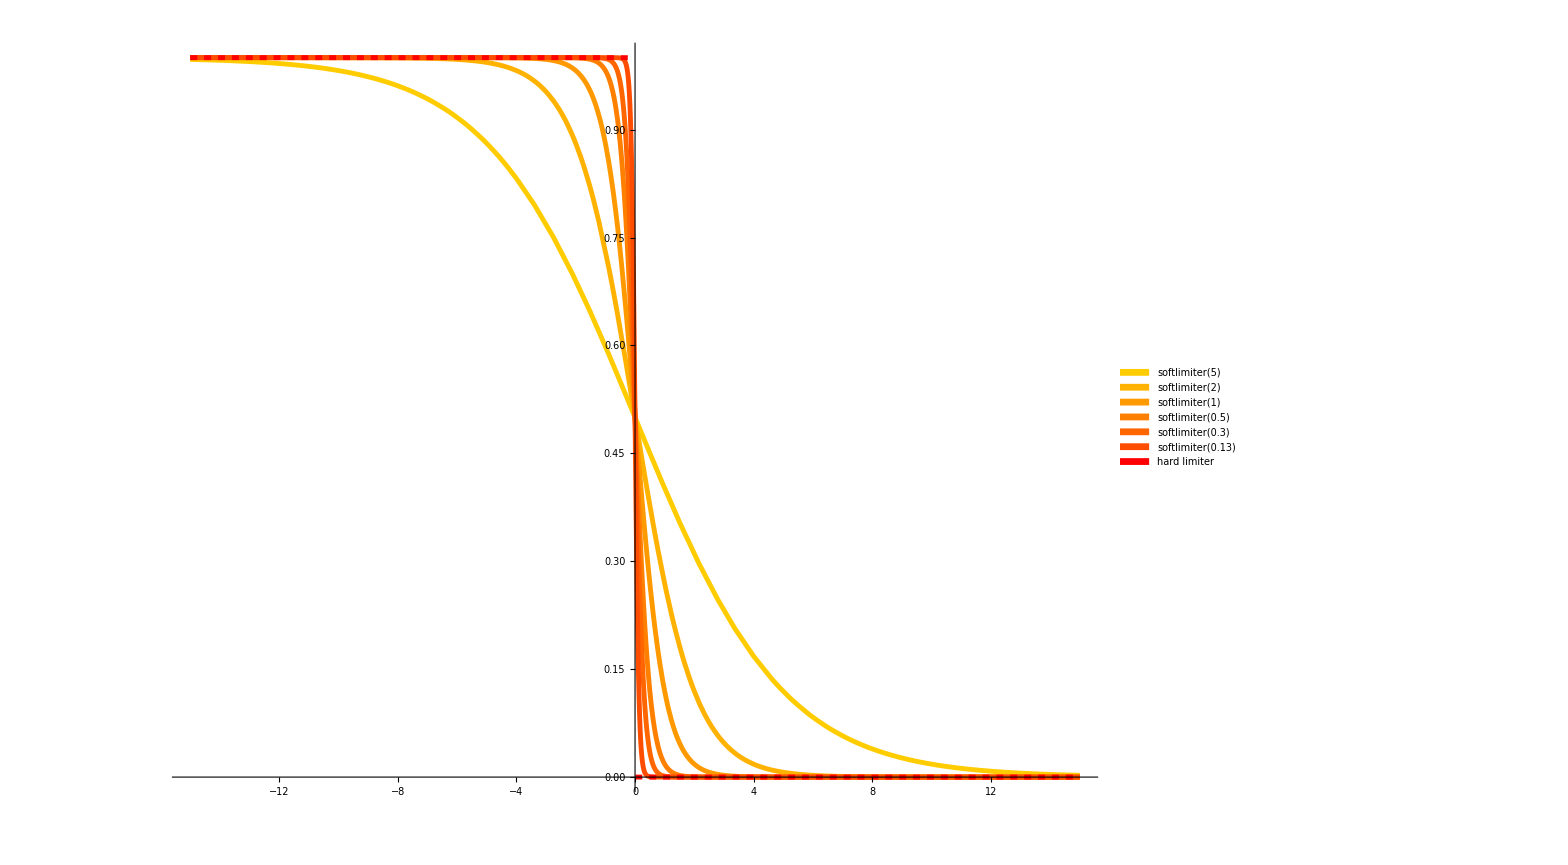

/media/leviathan/SPACE/meta/Work.Repositories/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/build/Limiter-softness-plot.png

```mathematica
Limiter softness plot
limitValue = 0;
imageName="Limiter-softness-plot";
imageSize = 1400;

hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_,softness_]:=(1/2)*(Tanh[ (limitValue-x)/softness]+1); (* A soft limiter using a tanh *)

lineThickness = 0.0025;
softnessPlot =Plot[{softLim[x,5],softLim[x,2],softLim[x,1],softLim[x,0.5],softLim[x,0.3],softLim[x,0.13],hardLim[x]},{x,-15,15},PlotStyle->{
{RGBColor[1,0.8,0],Thickness[lineThickness]},
{RGBColor[1,0.7,0],Thickness[lineThickness]},
{RGBColor[1,0.6,0],Thickness[lineThickness]},
{RGBColor[1,0.5,0],Thickness[lineThickness]},
{RGBColor[1,0.4,0],Thickness[lineThickness]},
{RGBColor[1,0.3,0],Thickness[lineThickness]},
{Red,Dashed,Thickness[lineThickness]}},
PlotLegends->Placed[SwatchLegend[{"softlimiter(5)","softlimiter(2)","softlimiter(1)","softlimiter(0.5)","softlimiter(0.3)","softlimiter(0.13)","hard limiter"},LabelStyle->{GrayLevel[0.3],FontSize->Scaled[.02]}],{0.9,0.5}],
BaseStyle->{FontSize->Scaled[.02]},
ImageSize->imageSize]

Export[baseImagePath<>imageName <> ".png",softnessPlot,Background->None]
```

```mathematica
Set current working directory to Notebook directory
SetDirectory[NotebookDirectory[]];
```

current directory^2 Notebook Set to working

```mathematica
NotebookDirectory[]
```

/home/leviathan/meta/Work.Repositories/git/minemonics/Minemonics/doc/measurements/